{n∈ℤ}

1

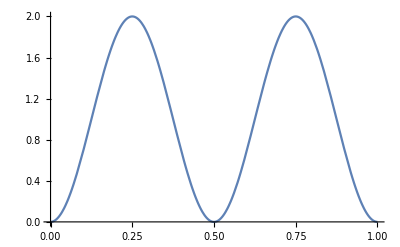

```mathematica
$Assumptions={n∈Integers}
ψx[n_][x_]:=2Sin[n π x]^2
Integrate[ψx[n][x],{x,0,1}]
Plot[ψx[2][x],{x,0,1}]
```

```mathematica
randomSample[n_?OddQ]:=With[
{
x=RandomReal[{0,1/2}],
y=RandomReal[{0,2}]
},
If[y<ψx[n][x],x,1/2+x]
]
randomSample[n_?EvenQ]:=With[
{
x=RandomReal[{0,1/2}],
y=RandomReal[{0,2}]
},
If[y<ψx[n][x],x,Mod[x+1/(2n),1/2]+1/2]
]
x[x0_,v0_][t_]:=Abs[1-Mod[x0+v0 t,2]]
xp[x0_,v0_][t_]:= Piecewise[{{-v0,1-Mod[t v0+x0,2]>0},{v0,True}}]
ensembleParams=Array[{randomSample[3],RandomChoice[{1,1}->{1,-1}]}&,10000];
ensemble={x@@#,xp@@#}&/@ensembleParams;
ensembleAt[t_]:={#[[1]][t],#[[2]][t]}&/@ensemble
ensembleXAt[t_]:=ensembleAt[t][[All,1]]
Manipulate[Histogram[ensembleXAt[t],{.05}],{t,0,1}]
```